```mathematica
Solve[-6==10 Log10[x],x]//N
```

{{x→0.251189}}

```mathematica
Sin[2π]
```

0

```mathematica
h[k_]:=Sin[.4 π (k-2)]/(π (k-2))
```

```mathematica
Table[h[i],{i,-2,2}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

{-0.0756827,-0.062366,0.0935489,0.302731,Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

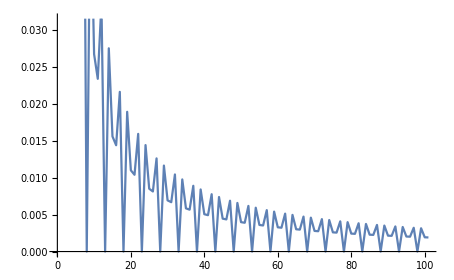

```mathematica
ListPlot[Abs[Table[h[i],{i,0,100}]],Joined->True]
```

```mathematica
FourierTransform[h[t],t,w]
```

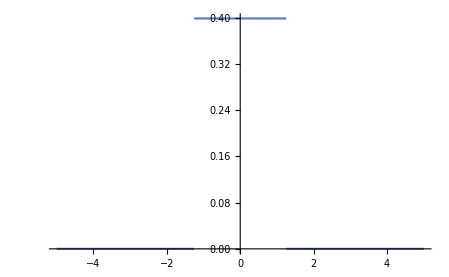

```mathematica
Plot[Abs[(-8.834874115176436*^-18+0.06349363593424096 ⅈ) (Cos[(2.+0. ⅈ) w]+ⅈ Sin[(2.+0. ⅈ) w]) ((-5.565832849343535*^-16+7.744623826707892*^-32 ⅈ)+1. Gamma[0,(0.-2.5132741228718345 ⅈ)+(0.+2. ⅈ) w]-(1.0000000000000004-2.0871873185038263*^-16 ⅈ) Gamma[0,(0.+2.5132741228718345 ⅈ)+(0.+2. ⅈ) w]+(1.0000000000000004-2.0871873185038263*^-16 ⅈ) Log[(0.-1.2566370614359172 ⅈ)-(0.+1. ⅈ) w]-(1.0000000000000004+6.957291061679412*^-17 ⅈ) Log[(0.+1.2566370614359172 ⅈ)-(0.+1. ⅈ) w]+(2.000000000000001+1.3914582123358823*^-16 ⅈ) Log[(0.-1.2566370614359172 ⅈ)+(0.+1. ⅈ) w]-(2.000000000000001-4.1743746370076527*^-16 ⅈ) Log[(0.+1.2566370614359172 ⅈ)+(0.+1. ⅈ) w]-(1.0000000000000004-2.0871873185038263*^-16 ⅈ) Derivative[1,0,0][Hypergeometric1F1][0,1.,(0.-2.5132741228718345 ⅈ)-(0.+2. ⅈ) w]+1. Derivative[1,0,0][Hypergeometric1F1][0,1.,(0.+2.5132741228718345 ⅈ)-(0.+2. ⅈ) w])],{w,-5,5}]
```

```mathematica
.4π//N
```

1.25664

```mathematica
h[t_]:=2*(.4 π)/(2π)Sinc[2(.4 π)/(2π)t]
```

```mathematica
FourierTransform[h[t],t,w]
```

1.25331+0. ⅈ

```mathematica
.4 π/(2 π)
```

0.2

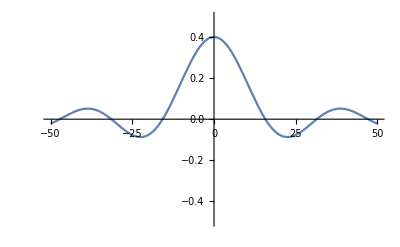

```mathematica
Plot[.4 Sinc[.2 t],{t,-50,50},PlotRange->{-.5,.5}]
```

```mathematica
FourierTransform[  Sin[4/10 π t]/(π t),t,w]
```

(1/2 √(π/2) Sign[(2 π)/5-w]+1/2 √(π/2) Sign[(2 π)/5+w])/π

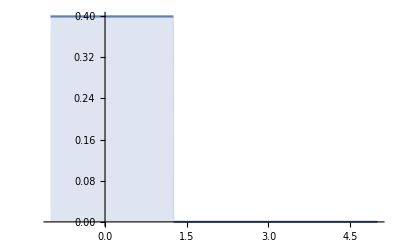

```mathematica
Plot[(1/2 √(π/2) Sign[(2 π)/5-w]+1/2 √(π/2) Sign[(2 π)/5+w])/π,{w,-1,5},Filling->Axis]
```

```mathematica
Table[.4 Sinc[.2 t],{t,-2,2}]
```

{0.389418,0.397339,0.4,0.397339,0.389418}

```mathematica
pi=π
```

π

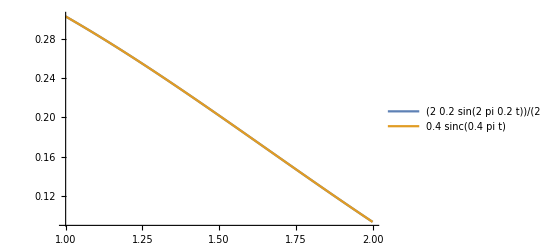

```mathematica
Plot[{2*.2 Sin[2pi .2t]/(2 pi .2 t),.4Sinc[.4pi t]},{t,1,2},PlotLegends->"Expressions"]
```

```mathematica
Sinc[4/10 t]
```

Sinc[(2 t)/5]

```mathematica
Table[.4Sinc[.4pi t],{t,-2,2}]
```

```mathematica
Round[{0.09354892837886393,0.30273069145626286,0.4,0.30273069145626286,0.09354892837886393},.1]
```

{0.1,0.3,0.4,0.3,0.1}